```mathematica
SetDirectory[NotebookDirectory[]];
<<mathutils.m;
(*<<ed5314utils_en.m;*)
<<kinematic_utils.m
<<MaTeX`
```

## Architecture of the CDPR

-Graphics-

```mathematica
roots={{−4.2220216376218525374,−5.9041632869515210360,−0.4719284164260346102,
+1.6804603696020390943,+3.5743047536049493407,+5.5605475750988856764},{−3.3553981637732204646,+0.5425359168641715099,+1.7110227662077546889,
+2.9313331749199504570,+4.0768903590846968732,+6.0451905744644536057},{−1.1658499286472699650,−1.2731250301592223731,−1.0066002786209496830,
+1.3992607683511133116,+3.2794852510182088478,+5.5312834538826469464},{−0.5483498696623835987,−0.4877188327940637588,−1.2105960172659885404,
+1.8159313811036966479,+4.3022189513770458215,+5.5516371755216273886},{−0.5044737581189470443,+2.5903097146888037712,−1.2479550929596409397,
+3.5231344366003843222,+5.5320236367500482920,+5.2626779413057278297},{+0.5434332197723969320,−0.1455056574282349313,+0.5696219999523911064,
+3.0240954483208687602,+4.7309738515237873056,+3.3019215367593690362}};
```

```mathematica
roots//MatrixForm
```

(-4.222021637621852537 | -5.904163286951521036 | -0.47192841642603461 | 1.680460369602039094 | 3.574304753604949341 | 5.560547575098885676
-3.355398163773220465 | 0.54253591686417151 | 1.711022766207754689 | 2.931333174919950457 | 4.076890359084696873 | 6.045190574464453606
-1.165849928647269965 | -1.273125030159222373 | -1.006600278620949683 | 1.399260768351113312 | 3.279485251018208848 | 5.531283453882646946
-0.548349869662383599 | -0.487718832794063759 | -1.21059601726598854 | 1.815931381103696648 | 4.302218951377045822 | 5.551637175521627389
-0.504473758118947044 | 2.590309714688803771 | -1.24795509295964094 | 3.523134436600384322 | 5.532023636750048292 | 5.26267794130572783
0.543433219772396932 | -0.145505657428234931 | 0.569621999952391106 | 3.02409544832086876 | 4.730973851523787306 | 3.301921536759369036)

```mathematica
phi={e1,e2,e3};
```

```mathematica
phimat={{0,-e3,e2},{e3,0,-e1},{-e2,e1,0}};
```

```mathematica
Rphi=Simplify[IdentityMatrix[3]+2*(((phimat)+(phimat.phimat))/(1+e1^2+e2^2+e3^2))];
```

```mathematica
A1={0,0,0};
A2={a2x,a2y,a2z};
A3={a3x,a3y,a3z};
```

```mathematica
b1d={b1x,b1y,b1z};
b2d={b2x,b2y,b2z};
b3d={b3x,b3y,b3z};
```

```mathematica
X={x,y,z};
```

```mathematica
r1=Rphi.b1d;
r2=Rphi.b2d;
r3=Rphi.b3d;
```

```mathematica
B1=X+r1;
B2=X+r2;
B3=X+r3;
```

```mathematica
s1=B1-A1;
s2=B2-A2;
s3=B3-A3;
```

```mathematica
n1=(({s1}.Transpose[{s1}])[[1,1]])-ρ1^2;
n2=(({s2}.Transpose[{s2}])[[1,1]])-ρ2^2;
n3=(({s3}.Transpose[{s3}])[[1,1]])-ρ3^2;
```

```mathematica
q1=Expand[Together[n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
q2=Expand[Together[n2-n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
q3=Expand[Together[n3-n1]*(1+e1^2+e2^2+e3^2)];
```

```mathematica
te=q3;
{Exponent[te, x], Exponent[te, y], Exponent[te, z], Exponent[te, e1], Exponent[te, e2], Exponent[te, e3]}
```

{1,1,1,2,2,2}

```mathematica
(*These give 3 equations in 6 variables. We need 3 more equations in only these 6 variables to be able to solve it*)
```

```mathematica
II={1,0,0};
JJ={0,1,0};
KK={0,0,1};
```

```mathematica
G0=X-KK;
```

```mathematica
Zero31={0,0,0};
```

```mathematica
Mo=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-A2,s2]}],Transpose[{Cross[-A3,s3]}],Transpose[{Cross[X,KK]}],2])];
```

```mathematica
MA2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-A2),s3]}],Transpose[{Cross[(X-A2),KK]}],2])];
```

```mathematica
MA3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-A3),s1]}],Transpose[{Cross[-(A2-A3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-A3),KK]}],2])];
```

```mathematica
MB1=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Zero31}],Transpose[{Cross[-(A2-B1),s2]}],Transpose[{Cross[-(A3-B1),s3]}],Transpose[{Cross[(X-B1),KK]}],2])];
```

```mathematica
MB2=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B2),s1]}],Transpose[{Zero31}],Transpose[{Cross[-(A3-B2),s3]}],Transpose[{Cross[(X-B2),KK]}],2])];
```

```mathematica
MB3=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-B3),s1]}],Transpose[{Cross[-(A2-B3),s2]}],Transpose[{Zero31}],Transpose[{Cross[(X-B3),KK]}],2])];
```

```mathematica
MG=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-X),s1]}],Transpose[{Cross[-(A2-X),s2]}],Transpose[{Cross[-(A3-X),s3]}],Transpose[{Cross[(X-X),KK]}],2])];
```

```mathematica
MG0=Join[(Join[Transpose[{-s1}],Transpose[{-s2}],Transpose[{-s3}],Transpose[{KK}],2]),(Join[Transpose[{Cross[-(A1-G0),s1]}],Transpose[{Cross[-(A2-G0),s2]}],Transpose[{Cross[-(A3-G0),s3]}],Transpose[{Cross[(X-G0),KK]}],2])];
```

```mathematica
MG0//Dimensions
```

{6,4}

```mathematica
p1=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[6;;6,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p2=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[5;;5,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
p3=Expand[Together[Det[Join[Mo[[1;;3,1;;4]],Mo[[4;;4,1;;4]]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p4=Expand[Together[Det[Mo[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p5=Expand[Together[Det[MB1[[4;;6,2;;4]]]]*((1+e1^2+e2^2+e3^2)^2)];
p6=Expand[Together[Det[Join[MB2[[4;;6,1;;1]],MB2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p7=Expand[Together[Det[Join[MA2[[4;;6,1;;1]],MA2[[4;;6,3;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p8=Expand[Together[Det[Join[MB3[[4;;6,1;;2]],MB3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p9=Expand[Together[Det[Join[MA3[[4;;6,1;;2]],MA3[[4;;6,4;;4]],2]]]*((1+e1^2+e2^2+e3^2)^2)];
p10=Expand[Together[Det[MG[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
p11=Expand[Together[Det[MG0[[4;;6,1;;3]]]]*((1+e1^2+e2^2+e3^2)^2)];
```

```mathematica
basedata={a2x-> 10,a2y-> 0,a2z-> 0,a3x-> 0,a3y-> 12,a3z-> 0};
platformdata={b1x-> 1,b1y-> 0,b1z-> 0,b2x-> 0,b2y-> 1,b2z-> 0,b3x-> 0,b3y-> 0,b3z-> 1};
cablelendata={ρ1-> 75/10,ρ2-> 10,ρ3-> 95/10};
numdata=Union[basedata,platformdata,cablelendata];
```

```mathematica
numdata
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1,ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
numdata2 = Union[basedata,platformdata]
```

{a2x→10,a2y→0,a2z→0,a3x→0,a3y→12,a3z→0,b1x→1,b1y→0,b1z→0,b2x→0,b2y→1,b2z→0,b3x→0,b3y→0,b3z→1}

```mathematica
q1n=q1/.numdata;
q2n=q2/.numdata;
q3n=q3/.numdata;
p1n=p1/.numdata;
p2n=p2/.numdata;p3n=p3/.numdata;p4n=p4/.numdata;p5n=p5/.numdata;p6n=p6/.numdata;p7n=p7/.numdata;p8n=p8/.numdata;p9n=p9/.numdata;p10n=p10/.numdata;p11n=p11/.numdata;
```

```mathematica
polys1={q1n,q2n,q3n,p1n,p2n,p3n,p4n,p5n,p6n,p7n,p8n,p9n,p10n,p11n};
```

```mathematica
ByteCount[polys1]/1024//N
```

270.742

```mathematica
polys1//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
polys1//Dimensions
```

{14}

```mathematica
(*We have in total of 14 equations in 6 variables.*)
```

```mathematica
(*Since we only need 6 equations for the 6 variables and also it is given that the obtained solutions are linearly independent but are nolinearly dependent. Assuming that this means that these might have additional terms multiplying the equations and hence selecting the lowest degree polynomials to obtain the FK solutions. We'll need to check if we cover all the solutions with this choice of polynomials*)
```

```mathematica
(*Working with p1, p2, p3 and q1, q2, q3*)
```

```mathematica
eqns = {q1n, q2n, q3n, p1n, p2n, p3n};
```

```mathematica
eqns//Variables
```

{e1,e2,e3,x,y,z}

```mathematica
eqns//Dimensions
```

{6}

```mathematica
(*Now we have 6 equations in 6 variables. But since it is underconstrained should something else be added? Assumption is that: Since we took equations from both geometric conditions and the statics, these solutions are definitely feasible, but 1. Needs to checked with the other polynomials to see if they also satisfy these solutions, 2. See if we obtain an additional set of unique solutions if a set of any other 3 equations are taken and verify that all the equations satisfy its. After this it should also be checked if the solutions have +ve tension. Or after one round of computation, take the tensions also as variables to be computed and use the 9 equations to solve for both x, y, z, e1, e2, e3, τ1, τ2, τ3 together*)
```

```mathematica
(*Starting with a reported FK solution*)
```

```mathematica
init = roots[[5]];
vars = {e1,e2,e3,x,y,z};
```

```mathematica
ambrule = Inner[Rule, vars, init, List];
```

```mathematica
initrule = Inner[Rule, vars, roots[[1]], List];
```

```mathematica
eqns/.initrule
```

{0.,0.,0.,0.,0.,0.}

```mathematica
polys1/.ambrule
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
q1n2=q1/.numdata2;
q2n2=q2/.numdata2;
q3n2=q3/.numdata2;
p1n2=p1/.numdata2;
p2n2=p2/.numdata2;
p3n2=p3/.numdata2;
p4n2=p4/.numdata2;
p5n2=p5/.numdata2;
p6n2=p6/.numdata2;
p7n2=p7/.numdata2;
p8n2=p8/.numdata2;
p9n2=p9/.numdata2;
```

```mathematica
η = {q1n2, q2n2, q3n2, p1n2, p2n2, p3n2};
Variables[η]
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
η//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
(*file=Import["CDPRC.txt","Text"]*)
```

```mathematica
cη = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[η], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
sym2 = {ρ1->rh1, ρ2->rh2, ρ3->rh3};
```

#### Numerical substitution rules:

```mathematica
(*inversetrig = Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
trigrules =  Union[{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
(*Rules for removing the greek symbols*)
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
(*Replacing all the cos, sin[ϕ's] and cos, sin[ψ's]*)
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
(*Most of the expressions have repeated sin and cosine which needs to be computed only once*)
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
replist=Union[{Power-> pow}, inversetrig, trigtoalg, nogreek];*)
```

```mathematica
ηc = Table[ToString[CForm[η[[i]]/.sym2]/.Power->pow],{i, Length[η]}];
```

```mathematica
Jn = D[η, {vars}];
Jn//Variables
```

{e1,e2,e3,x,y,z,ρ1,ρ2,ρ3}

```mathematica
Jη = Table[ToString[CForm[Flatten[Jn/.sym2][[i]]]/.Power->pow],{i, Length[Flatten[Jn]]}];
```

```mathematica
(*FileTemplateApply[file,<|"text"->Evaluate[ηc], "text2"->Evaluate[Jη]|>,"CDPRC_out.txt"]*)
```

```mathematica
cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{-1.27898×10^-13,1.7053×10^-13,1.13687×10^-13,-7.27596×10^-12,-3.97904×10^-12,-7.02016×10^-12}

```mathematica
cJn = Compile[{{e1, _Real},{e2, _Real},{e3, _Real},{x, _Real},{y, _Real}, {z, _Real}, {ρ1, _Real}, {ρ2, _Real}, {ρ3, _Real}}, Evaluate[Jn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]
```

{{8.33908,11.3826,-9.4952,53.0665,95.1285,92.3751},{-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526},{17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970616},{20601.9,3305.3,-2288.28,7929.13,2307.67,0.},{-8330.59,-2546.89,-15874.5,-3535.53,-6054.78,-1667.35},{4226.25,-6626.67,777.23,8318.58,2159.15,-1260.83}}

```mathematica
Flatten[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{8.33908,11.3826,-9.4952,53.0665,95.1285,92.3751,-44.4937,39.2052,114.428,-176.642,22.0144,-7.10526,17.9379,-57.3858,-72.663,26.9047,-229.212,-0.970616,20601.9,3305.3,-2288.28,7929.13,2307.67,0.,-8330.59,-2546.89,-15874.5,-3535.53,-6054.78,-1667.35,4226.25,-6626.67,777.23,8318.58,2159.15,-1260.83}

```mathematica
bla2 = (vars/.ambrule) - LinearSolve[cJn@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[(vars/.ambrule), {ρ1, ρ2, ρ3}/.cablelendata]]
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
{ρ1, ρ2, ρ3}/.cablelendata
```

{15/2,10,19/2}

```mathematica
cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.27898×10^-13,-2.27374×10^-13,1.98952×10^-13,9.43601×10^-12,-8.29914×10^-12,-8.08598×10^-12}

```mathematica
Inner[Rule, vars, bla2, List]
```

{e1→-0.504474,e2→2.59031,e3→-1.24796,x→3.52313,y→5.53202,z→5.26268}

```mathematica
η[[1]]/.Inner[Rule, vars, bla2, List]/.ρ1->7.5
```

1.13687×10^-13

```mathematica
CForm[η[[1]]/.sym2]/.Power->pow
```

1 + 2*x + 4*e1*e2*y + 4*e3*y - 4*e2*z + 4*e1*e3*z + pow(e1,2) + 2*x*pow(e1,2) + pow(e2,2) - 2*x*pow(e2,2) + pow(e3,2) - 2*x*pow(e3,2) - pow(rh1,2) - 
   pow(e1,2)*pow(rh1,2) - pow(e2,2)*pow(rh1,2) - pow(e3,2)*pow(rh1,2) + pow(x,2) + pow(e1,2)*pow(x,2) + pow(e2,2)*pow(x,2) + pow(e3,2)*pow(x,2) + pow(y,2) + 
   pow(e1,2)*pow(y,2) + pow(e2,2)*pow(y,2) + pow(e3,2)*pow(y,2) + pow(z,2) + pow(e1,2)*pow(z,2) + pow(e2,2)*pow(z,2) + pow(e3,2)*pow(z,2)

```mathematica
cablelendata
```

{ρ1→15/2,ρ2→10,ρ3→19/2}

```mathematica
η/.Inner[Rule, vars, bla2, List]/.cablelendata
```

{1.13687×10^-13,-1.13687×10^-13,3.41061×10^-13,3.63798×10^-12,1.81899×10^-12,9.09495×10^-12}

```mathematica
bla2
```

{-0.504474,2.59031,-1.24796,3.52313,5.53202,5.26268}

```mathematica
LinearSolve[cJn@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata], cη@@Join[bla2, {ρ1, ρ2, ρ3}/.cablelendata]]
```

{-5.31188×10^-16,2.65179×10^-15,3.31165×10^-16,1.98295×10^-15,-1.45202×10^-15,1.49594×10^-15}

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJn@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*7, 6, 5, *)
```

```mathematica
ambrule = Inner[Rule, vars, roots[[2]], List];
```

```mathematica
cη@@Join[vars/.ambrule, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
test = TrackRoot[{ρ1, ρ2, ρ3}/.cablelendata, vars/.ambrule]
```

{-3.355398163773220465,0.54253591686417151,1.711022766207754689,2.931333174919950457,4.076890359084696873,6.045190574464453606}

```mathematica
test-vars/.ambrule
```

{0.,0.,0.,0.,0.,0.}

```mathematica
(*Confirming the NR solution*)
```

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
(*Validating the solution for all the 15 equations*)
```

```mathematica
polys1/.Inner[Rule, vars, test, List]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Doing root tracking by using the linear-interpolation of the lengths*)
```

```mathematica
rinitial = {15/2, 10, 19/2};
rfinal = {10,11,8};
rinter = Table[rinitial+ii*(rfinal-rinitial),{ii, 0, 1, 0.001}];
```

```mathematica
parampath = rinitial+α*(rfinal-rinitial);
```

```mathematica
(*file = Import["rintervals.txt", "Text"]*)
```

```mathematica
(*FileTemplateApply[file,<|"vals"->Evaluate[Flatten[rinter]]|>,"rinterevals_out.txt"]*)
```

```mathematica
(*This gives the required poses*)
```

```mathematica
test
```

{-3.355398163773220465,0.54253591686417151,1.711022766207754689,2.931333174919950457,4.076890359084696873,6.045190574464453606}

```mathematica
tic[]
tempϕ = test;
ϕlist = {tempϕ};
For[i=2,i≤Length[rinter], i++, 
tempϕ = TrackRoot[rinter[[i]], tempϕ];
AppendTo[ϕlist, tempϕ];
]
toc[]
```

Actual time consumed: 0.14194 seconds.

CPU time consumed: 0.141948 seconds.

```mathematica
ϕlist[[-2]]
```

{-3.00718,-0.39633,0.514958,2.63347,6.49506,6.60757}

```mathematica
η/.Inner[Rule, vars, {0.33021470679474329568,0.21738356627514082708,0.3036570953313515453,4.1796667409640049229,7.4600793279904245026,3.4198883194007057007}, List]/.ρ1->10/.ρ2->11/.ρ3->8
```

{-3.8×10^-15,-1.1×10^-14,3.8×10^-14,3.5×10^-13,7.×10^-15,7.4×10^-13}

```mathematica
steps = Table[ii, {ii, 1, Length[ϕlist]}];
```

```mathematica
(*Plotting the motion variables x, y, z, c1, c2, c3*)
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=4; (*Magnification in axis and axis labesl*)
fontsize=40; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize];

Return[f1nonsing];
]
```

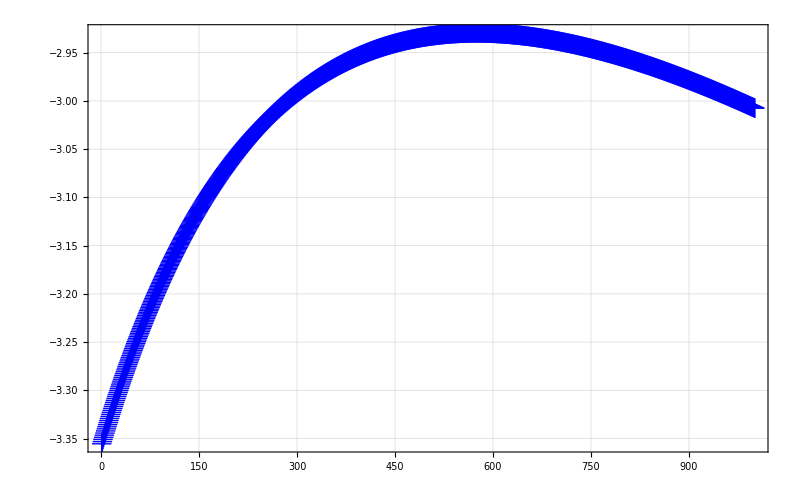

```mathematica
Texplot[steps, ϕlist[[;;, 1]], 800, "\\text{Discretisation step}", "x~\\text{coordinate}"]
```

```mathematica
Inner[Rule, vars, ϕlist[[-2]], List]
```

{e1→-3.00718,e2→-0.39633,e3→0.514958,x→2.63347,y→6.49506,z→6.60757}

```mathematica
ϕlist//Length
```

1001

```mathematica
rinter//Length
```

1001

```mathematica
(*Order of the error in the constraint equations*)
```

```mathematica
e1table= Table[Max[Abs[cη@@Join[ϕlist[[ii]], rinter[[ii]]]]], {ii, Length[ϕlist]}];
```

```mathematica
Max[e1table]
```

9.84031×10^-11

```mathematica
ambrule
```

{e1→-3.355398163773220465,e2→0.54253591686417151,e3→1.711022766207754689,x→2.931333174919950457,y→4.076890359084696873,z→6.045190574464453606}

```mathematica
paperval = {e1-> −3.3553981637732204646, e2-> 0.5425359168641715099, e3-> +1.7110227662077546889, x-> +2.9313331749199504570, y-> +4.0768903590846968732, z-> +6.0451905744644536057};
```

```mathematica
paperval = ambrule;
```

```mathematica
cη@@Join[vars/.paperval, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
cη@@Join[test, {ρ1, ρ2, ρ3}/.cablelendata]
```

{1.98952×10^-13,2.27374×10^-13,-3.41061×10^-13,-1.15961×10^-11,-1.59162×10^-11,2.54659×10^-11}

```mathematica
(*Visualisation*)
```

```mathematica
A1
```

{0,0,0}

```mathematica
ϕlist[[2]][[4;;]]
```

{2.93088,4.07896,6.04615}

```mathematica
(B1+B2+B3+X)/4/.sol/.numdata2
```

ReplaceAll::reps: {sol} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1/4 (1+(2 e1 e2-2 e3)/(1+e1^2+e2^2+e3^2)+(2 (e2+e1 e3))/(1+e1^2+e2^2+e3^2)-(2 (e2^2+e3^2))/(1+e1^2+e2^2+e3^2)+4 x),1/4 (1+(2 (e1 e2+e3))/(1+e1^2+e2^2+e3^2)-(2 (e1-e2 e3))/(1+e1^2+e2^2+e3^2)-(2 (e1^2+e3^2))/(1+e1^2+e2^2+e3^2)+4 y),1/4 (1-(2 (e1^2+e2^2))/(1+e1^2+e2^2+e3^2)+(2 (-e2+e1 e3))/(1+e1^2+e2^2+e3^2)+(2 (e1+e2 e3))/(1+e1^2+e2^2+e3^2)+4 z)}/.sol

```mathematica
ϕlist//Dimensions
```

{1001,6}

```mathematica
B1list = Table[B1/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B2list = Table[B2/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
B3list = Table[B3/.Inner[Rule, vars, ϕlist[[u]], List]/.numdata2,{u, 1, Length[ϕlist]}];
```

```mathematica
centerlist = (B1list+B2list+B3list+ϕlist[[;;,4;;]])/4;
```

```mathematica
sol = Inner[Rule, vars, ϕlist[[1]], List];
(*cables = Show[Graphics3D[{Thick, Red, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Green, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Blue,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;*)
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[1]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
(*pts = Table[Graphics3D[{Red, Sphere[ϕlist[[i]][[4;;]],  0.05]}, Boxed->False], {i, 1, u}];*)
(*pts2 = Table[Graphics3D[{Red, Sphere[centerlist[[i]],  0.05]}], {i, 1, u}];*)
Show[cables, base, tet, winches, fixtures, Axes->False,AxesOrigin->Automatic, AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}]
```

-Graphics3D-

```mathematica
Manipulate[
sol = Inner[Rule, vars, ϕlist[[u]], List];
(*cables = Show[Graphics3D[{Thick, Red, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Green, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Blue,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;*)
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[1]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
(*pts = Table[Graphics3D[{Red, Sphere[ϕlist[[i]][[4;;]],  0.05]}, Boxed->False], {i, 1, u}];*)
pts2 = Table[Graphics3D[{Red, Sphere[centerlist[[i]],  0.05]}], {i, 1, u}];
Show[pts2, cables, base, tet, winches, fixtures, Axes->False,AxesOrigin->Automatic, AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}],
{u, 1, Length[ϕlist],1}
]
```

```mathematica
(*Manipulate[
sol = Inner[Rule, vars, ϕlist[[u]], List];
(*cables = Show[Graphics3D[{Thick, Red, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Green, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Blue,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;*)
cables = Show[Graphics3D[{Thick, Black, Line[{A1, B1}]}, Boxed->False], Graphics3D[{Thick, Black, Line[{A2, B2}]}, Boxed->False], Graphics3D[{Thick, Black,Line[{A3, B3}]}, Boxed->False]]/.numdata/.sol;
base = Graphics3D[{Thick, Gray, Opacity[0.7], Triangle[{A1, A2, A3}/.numdata2]}, Boxed->False];
tet = Graphics3D[{Opacity[0.4], Thick, Blue, Tetrahedron[Join[{B1, B2, B3, X}/.sol/.numdata2, {ϕlist[[u]][[4;;]]}]]}, Boxed->False];
winches = Graphics3D[{Red, Sphere[{A1, A2, A3}, 0.5]} , Boxed->False]/.numdata2;
fixtures = Graphics3D[{Green, Sphere[{B1, B2, B3}, 0.2]} , Boxed->False]/.sol/.numdata2;
(*pts = Table[Graphics3D[{Red, Sphere[ϕlist[[i]][[4;;]],  0.05]}, Boxed->False], {i, 1, u}];*)
pts2 = Table[Graphics3D[{Red, Sphere[centerlist[[i]],  0.05], Boxed->False}], {i, 1, u}];
(*Show[pts2, base, cables, tet, winches, fixtures, Axes->False,AxesOrigin->Automatic,AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}]*)
Show[base,tet, fixtures, Axes->False,AxesOrigin->Automatic,AxesLabel-> {"x","y","z"},ImageSize->{800,600}, ViewAngle->0.2564917866864384,ViewCenter->{0.5,0.5,0.5},ViewPoint->{-5.257159306798439,0.9060886946712579,-1.0724236586347513},ViewVertical->{-0.24793061691158666,0.05462901510467381,-0.9672363102709355}, Boxed->False],
{u, 1, Length[ϕlist],1},ContentSize->{1000, 1000}
]*)
```

For the singularity event identifier to be useful we need an IKsol

Starting with the singularity event identification along this chosen path using the SEI function. Using the functions from the singularity_event_v3 file

```mathematica
(* Specify one branch of interest on which we are moving and try to warn if the branch will encounter a singularity. Also, try to locate the singularity (estimate it with reasonable accuracy) *)
```

```mathematica
(* finddistroots[allroots,intrestroot,qxORqfull]: Function to find the distance between the branch of interest and other branches *)
(* Description of the inputs:
	allroots - qfull for all the branches, at a particular instant
  intrestroot - The branch in which the manipulator is physically moving
	qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
finddistroots[allroots_,intrestroot_,qxORqfull_]:=
Module[{n,ii,dist},
n=Length[allroots];
dist={};
For[ii=1,ii≤n,ii++,
If[ii≠intrestroot,
If[qxORqfull==1,
(* True *)AppendTo[dist,Norm[allroots[[intrestroot]]-allroots[[ii]]]];,
(* False *)AppendTo[dist,Norm[(allroots[[intrestroot]]-allroots[[ii]])[[1;;6]]]];
];
];
];
Return[dist]
];
```

```mathematica
(* Function to find the coefficients to the fitting quadratic function, which will be used to estimate the singularity *)
(* Description of the inputs:
	xlist - A list of 3 values of the path parameter (input variable)
  ylist - A list of the corresponding 3 values of the distance (output variable) 
*)
(* Description of the output:
{a1,a2,a3} - The coefficients of the quadratic equation which is satisfied by the 3 input points. 
          Equation of the form a1*α^2+a2*α+a3=d where α is the input variable and d is the output variable. 
*)
findextrapfuncCoeff[xlist_,ylist_]:=
Module[{a1,a2,a3,eq,x,y,coeff},
eq=a1*x^2+a2*x+a3-y;
coeff=Solve[{(eq/.Inner[Rule,{x,y},{xlist[[1]],ylist[[1]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[2]],ylist[[2]]},List]),(eq/.Inner[Rule,{x,y},{xlist[[3]],ylist[[3]]},List])}=={0,0,0},{a1,a2,a3}];
Return[Flatten[{a1,a2,a3}/.coeff]];
];
```

```mathematica
NRTracking[thetai_, phii_, eta_, Jeta_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
(*Takes in eta and Jeta as compiled functions*)
nvec = eta@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[(Norm[nvec]≥ 10^-10)&&(loopcounter≤100),
loopcounter++;
Jmat =  Jeta@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = eta@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
NRallbranches[allbranches_,legvals_]:=
Module[{},
(*Return[Table[Join[NRTracking[legvals, allbranches[[ii]], cη, cJn],legvals],{ii,Length[allbranches]}]]*)
Return[Table[NRTracking[legvals, allbranches[[ii]], cη, cJn],{ii,Length[allbranches]}]]
];
```

```mathematica
(* Function to identify if a singularity is being encountered along the desired path. *)
(* Description of the inputs:
	allbranches - A table of qfull for all the branches at the initial instant
    intrestbranch - The branch in which the manipulator is physically moving
	pathparam - (α,initval,finalval,initstepsize)
	parampath - Path definition: The task space variables defined in terms of the path parameter
 qxORqfull - A binary variable to decide which among qx or qfull is to be used for calculating the distance betweent the roots
*)
singularityEventIdentifier[allbranches_,intrestbranch_,pathparam_,parampath_,qxORqfull_]:=
Module[{α,initval,finalval,stepsize,distroots,prevstep,cnt,alphaI,alphaIminus1,alphaIminus2,alphaIplus1,distI,distIminus1,distIminus2,deldist,delalpha,legvals,nextstep,predstep,grad,ii,singbranch,dvals,alphavals,extrapcoeff,extrapfunc,a1,a2,a3,solSing,estiqxSing,estialphaSing,estiqfullSing,singFlag,returnval},
(* Defining a vector to store the distance between the branch of intrest and other branches *)
distroots={};
prevstep=allbranches;
{α,initval,finalval,stepsize}=pathparam;
(* At cnt=1, *)
alphaIminus1=initval;
alphaIminus2=initval;
(* Using only the task space variable to find the distance between the roots *)
distIminus1=finddistroots[prevstep,intrestbranch,qxORqfull];
distIminus2=distIminus1;
singFlag=0;
While[singFlag==0&&alphaIminus1<finalval,
alphaI=alphaIminus1+stepsize;
If[alphaI<finalval,alphaIplus1=alphaI+stepsize,alphaIplus1=finalval];
delalpha=alphaI-alphaIminus1;
legvals=parampath/.{α->alphaI};
nextstep=NRallbranches[prevstep,legvals];
distI=finddistroots[nextstep,intrestbranch,0];
deldist=distI-distIminus1;
grad=Table[deldist[[ii]]/delalpha,{ii,1,Length[distI]}];
predstep=Table[distI[[ii]]+(alphaIplus1-alphaI)*grad[[ii]],{ii,1,Length[grad]}];
For[ii=0,ii≤Length[predstep],ii++,
If[predstep[[ii]]<0,
singFlag=1;
singbranch=ii;
Print["Singularity encountered, branches ",intrestbranch," and ",singbranch," are observed to merge."];
dvals={distIminus2[[singbranch]],distIminus1[[singbranch]],distI[[singbranch]]};
alphavals={alphaIminus2,alphaIminus1,alphaI};
extrapcoeff=findextrapfuncCoeff[alphavals,dvals];
extrapfunc=a1*α^2+a2*α+a3/.Inner[Rule,{a1,a2,a3},extrapcoeff,List];
solSing=Solve[extrapfunc==0,α];
estialphaSing=If[(α/.solSing[[1]])-alphaI<(α/.solSing[[2]])-alphaI,solSing[[1]],solSing[[2]]];
estiqxSing=parampath/.estialphaSing;
(*estiqfullSing=Join[estiqxSing,iksolC[estiqxSing]];*)
returnval={singFlag,singbranch,estiqxSing};
];
];
If[singFlag==0,
alphaIminus2=alphaIminus1;
alphaIminus1=alphaI;
prevstep=nextstep;
If[alphaIminus1==finalval,
returnval={0,Null,Null};
Print["No singularity encountered"]
];
distIminus2=distIminus1;
distIminus1=distI;,
Break;
];
];
Return[returnval];
];
```

```mathematica
initpathparam = {α, 0, 0.5, 0.0001};
initinterestbranch = 2;
initparampath = parampath;
initqxorqfull = 0;
```

```mathematica
bla = singularityEventIdentifier[roots,initinterestbranch,initpathparam,initparampath,initqxorqfull]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-7220.81,5251.03,-3763.08,338779.,988974.,-2.59565×10^6},{24221.1,-34349.5,18210.5,-3.74083×10^6,481011.,-212158.},{19815.1,-56391.,«3»,-394399.},{«1»},{-8.08011×10^9,1.60356×10^11,-1.28013×10^10,2.38602×10^12,2.04291×10^12,2.68274×10^12},{7.38276×10^10,2.12146×10^10,3.98109×10^10,-3.43446×10^12,-2.36722×10^12,-1.31061×10^12}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-415306.,206342.,-3.92261×10^6,-2.51422×10^8,-2.28356×10^8,-1.4756×10^8},{-495409.,216199.,-2.1738×10^6,-1.15662×10^8,-1.25435×10^7,-4.81799×10^6},{-368823.,«4»,8.50315×10^6},{«1»},{3.80829×10^14,-2.62542×10^14,3.99054×10^14,1.07668×10^16,1.81528×10^15,2.1583×10^16},{-2.81189×10^14,1.19691×10^14,3.17247×10^14,1.43772×10^15,7.76872×10^15,1.07868×10^16}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{-4.23513×10^7,-7.18045×10^7,-1.26564×10^7,1.05316×10^10,-4.22339×10^9,-2.61712×10^10},{4.27892×10^6,8.65081×10^6,2.64001×10^6,-4.86249×10^9,-2.22885×10^8,6.683×10^7},{-7.40929×10^6,«4»,-«21»},{«1»},{-1.40182×10^17,-1.71149×10^17,-3.84213×10^15,7.1782×10^19,1.02104×10^19,-1.64004×10^19},{-7.48834×10^16,5.56413×10^16,-5.34051×10^16,1.9194×10^19,-5.11223×10^18,3.27484×10^18}} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

Singularity encountered, branches 2 and 3 are observed to merge.

{1,3,{7.72175,10.0887,9.36695}}